## Previous Analysis:

2D Approximations:

## High Occupancy Data:

```mathematica
R100D00B00=Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R100D00B00.txt","Data"][[2;;]];
R8DE3B01 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8DE-3B0.1.txt","Data"][[2;;]];
R8DE6B01C1E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C1e3.txt","Data"][[2;;]];
R8DE6B01C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C1e4.txt","Data"][[2;;]];
R8DE6B01C2E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C2e4.txt","Data"][[2;;]];
R8DE6B01C5E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C5e4.txt","Data"][[2;;]];
R8DE6B02C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B02C1e4.txt","Data"][[2;;]];
R8DE6B005C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B005C1e4.txt","Data"][[2;;]];
R8DE6B05C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B05C1e4.txt","Data"][[2;;]];
R8DE7B005C1E4 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-7B005C1e4.txt","Data"][[2;;]];
R50DE6B005C1E4 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R50De-6B005C1e4.txt","Data"][[2;;]];
```

```mathematica
nlmR100D00B00 = NonlinearModelFit[R100D00B00,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE3B01 = NonlinearModelFit[R8DE3B01,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01CE3 = NonlinearModelFit[R8DE6B01CE3,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01CE4 = NonlinearModelFit[R8DE6B01CE4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01C2E4 = NonlinearModelFit[R8DE6B01C2E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01C5E4 = NonlinearModelFit[R8DE6B01C5E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B02C1E4 = NonlinearModelFit[R8DE6B02C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B05C1E4 = NonlinearModelFit[R8DE6B05C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE7B005C1E4 = NonlinearModelFit[R8DE7B005C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR50DE6B005C1E4 = NonlinearModelFit[R50DE6B005C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
```

```mathematica
nlmR100D00B00["ParameterTable"]nlmR8DE3B01["ParameterTable"]nlmR8DE6B01CE3["ParameterTable"]nlmR8DE6B01CE4["ParameterTable"]nlmR8DE6B01C2E4["ParameterTable"]nlmR8DE6B01C5E4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | -0.0726853 | 0.00392955 | -18.4971 | 3.23097×10^-43
B | -0.32088 | 0.00444563 | -72.1788 | 3.21725×10^-133
k | 1.03649 | 0.025305 | 40.9597 | 3.17957×10^-92
θ | 1.37737 | 0.0392454 | 35.0962 | 1.20252×10^-81  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0687146 | 0.00203984 | -33.6862 | 6.66736×10^-79
B | -0.32668 | 0.00232891 | -140.271 | 2.32922×10^-183
k | 1.02025 | 0.0125062 | 81.5794 | 2.34434×10^-142
θ | 1.38585 | 0.0191353 | 72.4237 | 1.80141×10^-133  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0684222 | 0.00288628 | -23.706 | 8.09071×10^-57
B | -0.323064 | 0.00322515 | -100.17 | 8.39263×10^-158
k | 1.03042 | 0.0177586 | 58.0238 | 4.04001×10^-117
θ | 1.36171 | 0.0270563 | 50.3288 | 8.31409×10^-107  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0674375 | 0.00288144 | -23.4041 | 4.53146×10^-56
B | -0.327485 | 0.00329887 | -99.272 | 4.0202×10^-157
k | 1.016 | 0.0174918 | 58.0842 | 3.39115×10^-117
θ | 1.38951 | 0.0266682 | 52.1035 | 2.65127×10^-109  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.065784 | 0.00150634 | -43.6713 | 1.03801×10^-96
B | -0.328361 | 0.00172668 | -190.169 | 1.34462×10^-206
k | 1.00999 | 0.00898028 | 112.467 | 1.44674×10^-166
θ | 1.39094 | 0.0136048 | 102.239 | 2.39492×10^-159  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0457538 | 0.0133665 | -3.42303 | 0.000769346
B | -0.309433 | 0.0130194 | -23.767 | 5.72079×10^-57
k | 1.08977 | 0.0775262 | 14.0568 | 1.25777×10^-30
θ | 1.18232 | 0.112461 | 10.5131 | 2.15746×10^-20

## Low Occupancy Data (λ = 0.05):

### Change Dark Rate:

```mathematica
DE3L005 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8DE-3B005C1e5L005.txt","Data"][[2;;]];
DE6 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8DE-6B005C1e5L01.txt","Data"][[2;;]];
DE7 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8DE-7B005C1e5L01.txt","Data"][[2;;]];
DE5 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-5B005C1e5L01.txt","Data"][[2;;]];
DE72 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8DE-7B005C1e5L01.txt","Data"][[2;;]];
DE4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-4B005C1e5L01.txt","Data"][[2;;]];
DE3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-3B005C1e5L01.txt","Data"][[2;;]];
DE2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-2B005C1e5L01.txt","Data"][[2;;]];
D2E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8D2e-2B005C1e5L01.txt","Data"][[2;;]];
D5E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8D5e-3B005C1e5L01.txt","Data"][[2;;]];
```

```mathematica
nlmD2E2= NonlinearModelFit[D2E2,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE2 = NonlinearModelFit[DE2,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmD5E3= NonlinearModelFit[D5E3,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
(*nlmDE3L005 = NonlinearModelFit[DE3L005,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];*)
nlmDE3 = NonlinearModelFit[DE3,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE4 = NonlinearModelFit[DE4,Centre+Amplitude Sin[Frequency ϕ+Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE5 = NonlinearModelFit[DE5,Centre+Amplitude Sin[Frequency ϕ+Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE6 = NonlinearModelFit[DE6,Centre+Amplitude Sin[Frequency ϕ+Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE7 = NonlinearModelFit[DE7,Centre +Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE72 = NonlinearModelFit[DE72,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
```

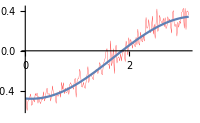
D = 2×10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | -0.0677332 | 0.0124323 | -5.44816 | 1.6849×10^-7
Amplitude | -0.412933 | 0.0152001 | -27.1664 | 4.81755×10^-65
Frequency | 0.993312 | 0.0623444 | 15.9327 | 4.99303×10^-36
Phase | 1.45914 | 0.097129 | 15.0227 | 2.03151×10^-33

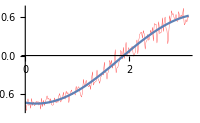
D = 10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | -0.0506676 | 0.0210715 | -2.40455 | 0.0172238
Amplitude | -0.705899 | 0.0233466 | -30.2356 | 8.06524×10^-72
Frequency | 0.977777 | 0.0499966 | 19.5569 | 4.22752×10^-46
Phase | 1.36291 | 0.0713052 | 19.1138 | 6.68069×10^-45

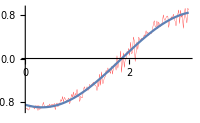
D = 5×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | -0.016277 | 0.0184014 | -0.884554 | 0.377597
Amplitude | -0.88003 | 0.0185771 | -47.3717 | 1.79699×10^-102
Frequency | 1.03547 | 0.0345512 | 29.9693 | 2.99348×10^-71
Phase | 1.23971 | 0.0486892 | 25.4617 | 4.5142×10^-61

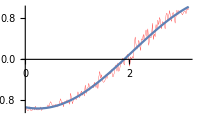
D = 10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.131385 | 0.0383033 | 3.43011 | 0.000750773
Amplitude | -1.09161 | 0.0404651 | -26.9766 | 1.31021×10^-64
Frequency | 0.875004 | 0.0391258 | 22.3639 | 1.87396×10^-53
Phase | 1.35787 | 0.0477838 | 28.4169 | 7.32924×10^-68

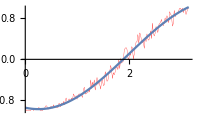
D = 10^-4 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.0929922 | 0.0307552 | 3.02363 | 0.00286893
Amplitude | -1.06597 | 0.0324884 | -32.8108 | 3.71574×10^-77
Frequency | 0.910436 | 0.0357582 | 25.4609 | 4.53434×10^-61
Phase | 1.33943 | 0.0454983 | 29.4392 | 4.16963×10^-70

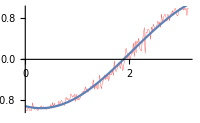
D = 10^-5 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.153735 | 0.0381198 | 4.03295 | 0.0000817801
Amplitude | -1.10773 | 0.0390987 | -28.3315 | 1.13478×10^-67
Frequency | 0.900004 | 0.0384262 | 23.4216 | 4.09933×10^-56
Phase | 1.30185 | 0.0467607 | 27.8406 | 1.42458×10^-66

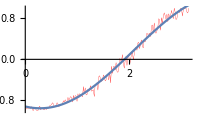
D = 10^-6 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.157462 | 0.0382044 | 4.12157 | 0.0000577388
Amplitude | -1.11379 | 0.0394105 | -28.2613 | 1.62722×10^-67
Frequency | 0.881513 | 0.0367427 | 23.9916 | 1.60244×10^-57
Phase | 1.31905 | 0.0440045 | 29.9754 | 2.90522×10^-71

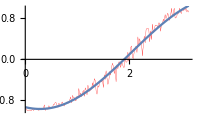
D = 10^-7 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.126345 | 0.0370528 | 3.40987 | 0.000805011
Amplitude | -1.09601 | 0.038338 | -28.5882 | 3.05736×10^-68
Frequency | 0.899269 | 0.0385289 | 23.3401 | 6.53839×10^-56
Phase | 1.31578 | 0.0473277 | 27.8014 | 1.74538×10^-66

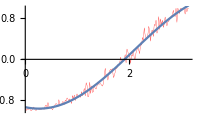
D = 10^-7(2) -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.157533 | 0.0408669 | 3.85479 | 0.000161897
Amplitude | -1.12067 | 0.0426512 | -26.2751 | 5.49907×10^-63
Frequency | 0.867946 | 0.0386502 | 22.4565 | 1.08993×10^-53
Phase | 1.34398 | 0.0461684 | 29.1103 | 2.17136×10^-69

```mathematica
"D = 2×10^-2" nlmD2E2["ParameterTable"]Show[ListLinePlot[D2E2,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmD2E2],{ϕ,0,π}]]
"D = 10^-2" nlmDE2["ParameterTable"]Show[ListLinePlot[DE2,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE2],{ϕ,0,π}]]
(*"D = 10^-3" nlmDE3L005["ParameterTable"]Show[ListLinePlot[DE3L005,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE3L005],{ϕ,0,π}]]
*)
"D = 5×10^-3" nlmD5E3["ParameterTable"]Show[ListLinePlot[D5E3,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmD5E3],{ϕ,0,π}]]
"D = 10^-3" nlmDE3["ParameterTable"]Show[ListLinePlot[DE3,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE3],{ϕ,0,π}]]
"D = 10^-4" nlmDE4["ParameterTable"]Show[ListLinePlot[DE4,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE4],{ϕ,0,π}]]
"D = 10^-5" nlmDE5["ParameterTable"]Show[ListLinePlot[DE5,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE5],{ϕ,0,π}]]
"D = 10^-6" nlmDE6["ParameterTable"]Show[ListLinePlot[DE6,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE6],{ϕ,0,π}]]
"D = 10^-7" nlmDE7["ParameterTable"]Show[ListLinePlot[DE7,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE7],{ϕ,0,π}]]
"D = 10^-7(2)" nlmDE72["ParameterTable"]Show[ListLinePlot[DE72,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE72],{ϕ,0,π}]]
```

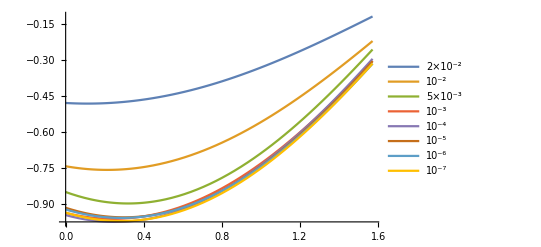

```mathematica
Plot[{Normal[nlmD2E2],Normal[nlmDE2],Normal[nlmD5E3],Normal[nlmDE3],Normal[nlmDE4],Normal[nlmDE5],Normal[nlmDE6],Normal[nlmDE7]},{ϕ,0,π/2},PlotLegends->{"2×10^-2","10^-2","5×10^-3","10^-3","10^-4","10^-5","10^-6","10^-7"}]
```

### Change Quantum Efficiency:

```mathematica
R10CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R10D00B005C1e5L01.txt","Data"][[2;;]];
R10CE6 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R10D00B005C1e6L01.txt","Data"][[2;;]];
R25CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R25D00B005C1e5L01.txt","Data"][[2;;]];
R50CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R50D00B005C1e5L01.txt","Data"][[2;;]];
R100CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R100D00B005C1e5L01.txt","Data"][[2;;]];
```

```mathematica
nlmR10CE5 = NonlinearModelFit[R10CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR10CE6 = NonlinearModelFit[R10CE6,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR25CE5 = NonlinearModelFit[R25CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR50CE5 = NonlinearModelFit[R50CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR100CE5 = NonlinearModelFit[R100CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
```

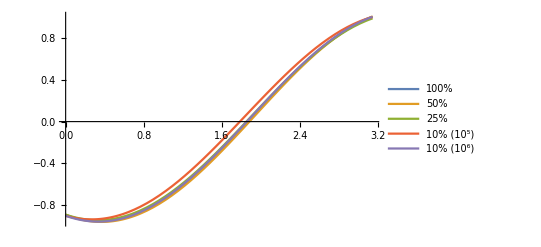

```mathematica
Plot[{Normal[nlmR100CE5],Normal[nlmR50CE5],Normal[nlmR25CE5],Normal[nlmR10CE5],Normal[nlmR10CE6]},{ϕ,0,π},PlotLegends->{"100%","50%","25%","10% (10^5)","10% (10^6)"}]
```

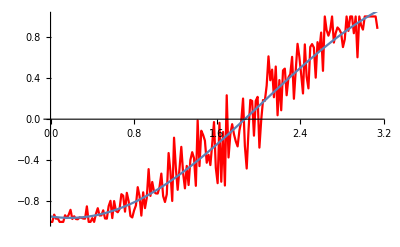

```mathematica
Show[ListLinePlot[R25CE5,PlotStyle->Red],Plot[Normal[nlmR25CE5],{ϕ,0,π}]]
```

```mathematica
2Sqrt[2+2/Sqrt[2]]
```

2 √(2+√2)

```mathematica
N[%]
```

3.69552

Spherical Locations:

### Changing the Dark Rate:

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
D1E6 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Spherical Data\\R8_D1e-06_B005_C1e+05_L01.txt","Data"][[2;;]];
D1E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Spherical Data\\R8_D1e-03_B005_C1e+05_L01.txt","Data"][[2;;]];
D2E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Spherical Data\\R8_D2e-03_B005_C1e+05_L01.txt","Data"][[2;;]];
D5E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Spherical Data\\R8_D5e-03_B005_C1e+05_L01.txt","Data"][[2;;]];
D1E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Spherical Data\\R8_D1e-02_B005_C1e+05_L01.txt","Data"][[2;;]];
D2E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Spherical Data\\R8_D2e-02_B005_C1e+05_L01.txt","Data"][[2;;]];
```

```mathematica
nlmD1E6 = NonlinearModelFit[D1E6,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD1E3 = NonlinearModelFit[D1E3,(*Centre*)-Amplitude Cos[(*Frequency *)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD2E3 = NonlinearModelFit[D2E3,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD5E3 = NonlinearModelFit[D5E3,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD1E2 = NonlinearModelFit[D1E2,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD2E2 = NonlinearModelFit[D2E2,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
```

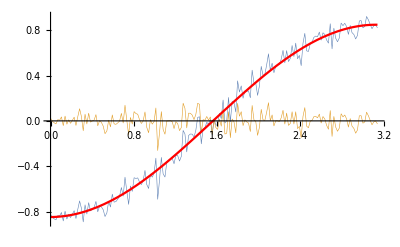
D = 1×10^-6 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 8.3361×10^-19 | 0. | 1.
Amplitude | 0.848389 | 0.00716194 | 118.458 | 1.67106×10^-170
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.00959587 | 0.00848856 | 1.13045 | 0.259817

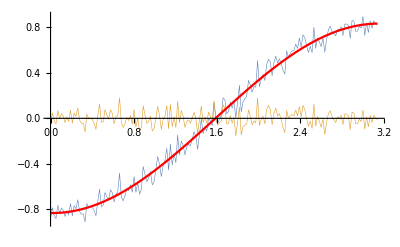
D = 1×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.45623×10^-18 | 0. | 1.
Amplitude | 0.831542 | 0.00687458 | 120.959 | 4.33029×10^-172
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0140164 | 0.00831304 | -1.68608 | 0.0935429

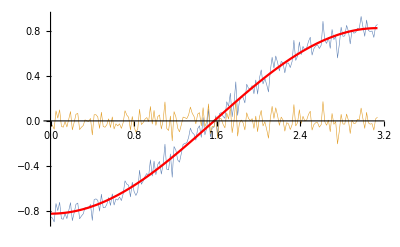
D = 2×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 2.01227×10^-18 | 0. | 1.
Amplitude | 0.824992 | 0.00725312 | 113.743 | 2.01807×10^-167
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.00153104 | 0.00884044 | -0.173186 | 0.862703

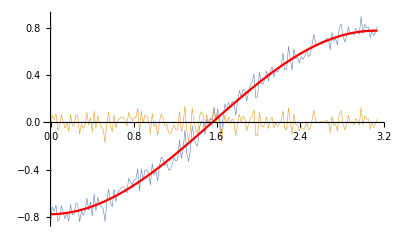
D = 5×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.60094×10^-18 | 0. | 1.
Amplitude | 0.775188 | 0.00643148 | 120.53 | 8.05535×10^-172
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.0175699 | 0.00834259 | 2.10605 | 0.0366101

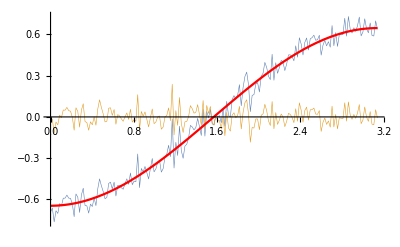
D = 1×10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.56847×10^-18 | 0. | 1.
Amplitude | 0.646205 | 0.00665869 | 97.0468 | 2.0685×10^-155
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.00228461 | 0.0103614 | 0.220493 | 0.825741

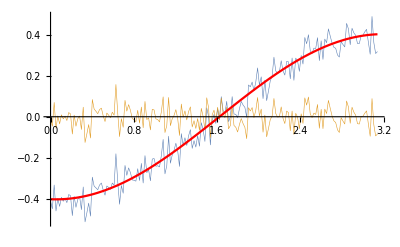
D = 2×10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 2.95162×10^-18 | 0. | 1.
Amplitude | 0.402708 | 0.00529675 | 76.0292 | 4.33153×10^-137
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.052636 | 0.0132253 | -3.97996 | 0.00010044

```mathematica
"D = 1×10^-6" nlmD1E6["ParameterTable"]Show[ListLinePlot[{D1E6,nlmD1E6["FitResiduals"]},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->400],Plot[Normal[nlmD1E6],{ϕ,0,π},PlotStyle->Red]]
"D = 1×10^-3" nlmD1E3["ParameterTable"]Show[ListLinePlot[{D1E3,nlmD1E3["FitResiduals"]},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->400],Plot[Normal[nlmD1E3],{ϕ,0,π},PlotStyle->Red]]
"D = 2×10^-3" nlmD2E3["ParameterTable"]Show[ListLinePlot[{D2E3,nlmD2E3["FitResiduals"]},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->400],Plot[Normal[nlmD2E3],{ϕ,0,π},PlotStyle->Red]]
"D = 5×10^-3" nlmD5E3["ParameterTable"]Show[ListLinePlot[{D5E3,nlmD5E3["FitResiduals"]},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->400],Plot[Normal[nlmD5E3],{ϕ,0,π},PlotStyle->Red]]
"D = 1×10^-2" nlmD1E2["ParameterTable"]Show[ListLinePlot[{D1E2,nlmD1E2["FitResiduals"]},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->400],Plot[Normal[nlmD1E2],{ϕ,0,π},PlotStyle->Red]]
"D = 2×10^-2" nlmD2E2["ParameterTable"]Show[ListLinePlot[{D2E2,nlmD2E2["FitResiduals"]},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->400],Plot[Normal[nlmD2E2],{ϕ,0,π},PlotStyle->Red]]
```

```mathematica
AmpD1E6 = nlmD1E6["ParameterTable"][[1,1,3,2]];
AmpD1E3 = nlmD1E3["ParameterTable"][[1,1,3,2]];
AmpD2E3 = nlmD2E3["ParameterTable"][[1,1,3,2]];
AmpD5E3 = nlmD5E3["ParameterTable"][[1,1,3,2]];
AmpD1E2 = nlmD1E2["ParameterTable"][[1,1,3,2]];
AmpD2E2 = nlmD2E2["ParameterTable"][[1,1,3,2]];
```

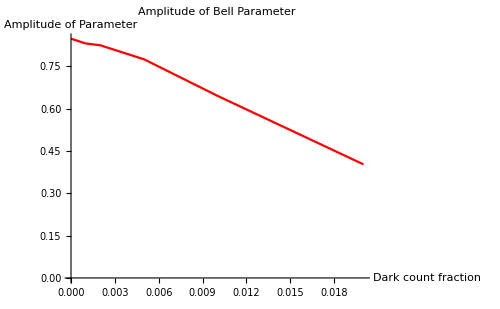

```mathematica
Amps = {{10^-6,AmpD1E6},{10^-3,AmpD1E3},{2 10^-3,AmpD2E3},{5 10^-3,AmpD5E3},{10^-2,AmpD1E2},{2 10^-2,AmpD2E2}};
ListLinePlot[Amps,PlotLabel->"Amplitude of Bell Parameter",AxesLabel->{"Dark count fraction","Amplitude of Parameter"},PlotStyle->Red,ImageSize->500]
```

## Corrected Functions:

#### Change Quantum Efficiency:

```mathematica
R100 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R100_D1e-06_B005_C1e+05_L01.txt","Data"][[2;;]];
R50 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R50_D1e-06_B005_C1e+05_L01.txt","Data"][[2;;]];
R20 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R20_D1e-06_B005_C1e+05_L01.txt","Data"][[2;;]];
R8 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B005_C1e+05_L01.txt","Data"][[2;;]];
R82 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B005_C2e+05_L01.txt","Data"][[2;;]];
```

```mathematica
nlmR100=NonlinearModelFit[R100,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmR50=NonlinearModelFit[R50,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmR20=NonlinearModelFit[R20,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmR8=NonlinearModelFit[R8,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmR82=NonlinearModelFit[R82,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
```

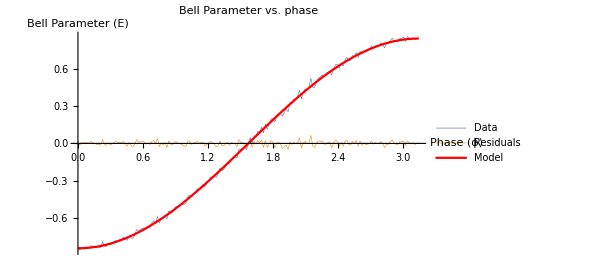
QE = 100% -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 6.6477×10^-19 | 0. | 1.
Amplitude | 0.839907 | 0.00186599 | 450.113 | 1.12631×10^-272
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.0000590666 | 0.00223397 | 0.0264402 | 0.978936

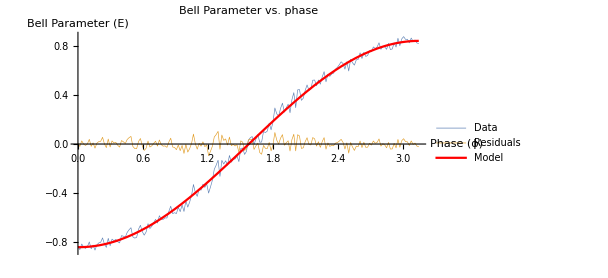
QE = 50% -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 7.30661×10^-19 | 0. | 1.
Amplitude | 0.843264 | 0.00386398 | 218.237 | 3.89698×10^-217
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.00415678 | 0.00460754 | -0.902169 | 0.368193

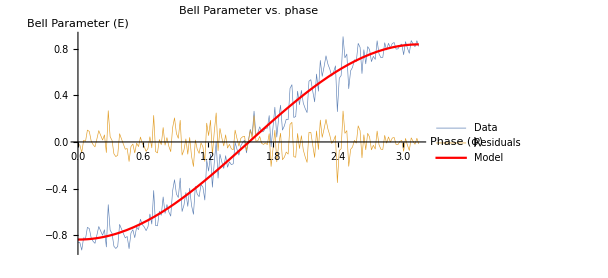
QE = 20% -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 2.23989×10^-18 | 0. | 1.
Amplitude | 0.83583 | 0.0101734 | 82.1587 | 6.91813×10^-143
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.00567325 | 0.012239 | -0.46354 | 0.643547

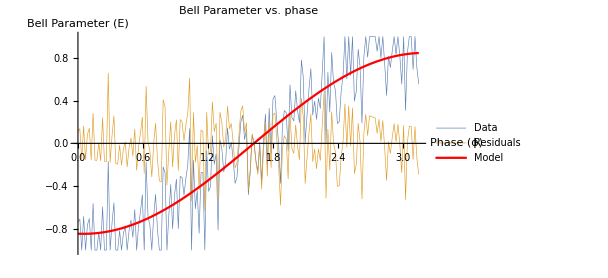
QE = 8% -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.23094×10^-17 | 0. | 1.
Amplitude | 0.847473 | 0.025916 | 32.7008 | 6.19329×10^-77
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0513126 | 0.0307488 | -1.66877 | 0.0969312

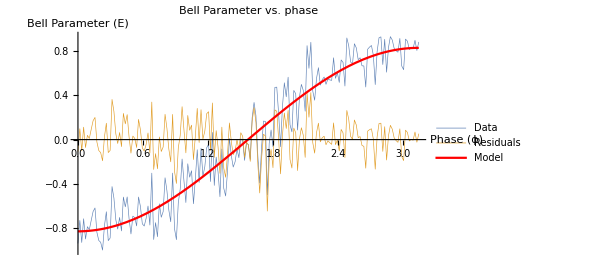
QE = 8% (2) -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 7.36896×10^-18 | 0. | 1.
Amplitude | 0.830202 | 0.0178276 | 46.5684 | 2.96516×10^-101
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.00389201 | 0.0215927 | 0.180246 | 0.857165

```mathematica
"QE = 100%" nlmR100["ParameterTable"]Show[ListLinePlot[{R100,nlmR100["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmR100],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"QE = 50%" nlmR50["ParameterTable"]Show[ListLinePlot[{R50,nlmR50["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmR50],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"QE = 20%" nlmR20["ParameterTable"]Show[ListLinePlot[{R20,nlmR20["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmR20],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"QE = 8%" nlmR8["ParameterTable"]Show[ListLinePlot[{R8,nlmR8["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmR8],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"QE = 8% (2)" nlmR82["ParameterTable"]Show[ListLinePlot[{R82,nlmR82["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmR82],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{Style["Phase (ϕ)",Black,15],Style["Bell Parameter (E)",Black,15]},PlotLabel->Style["Bell Parameter vs. phase",Black,20]]
```

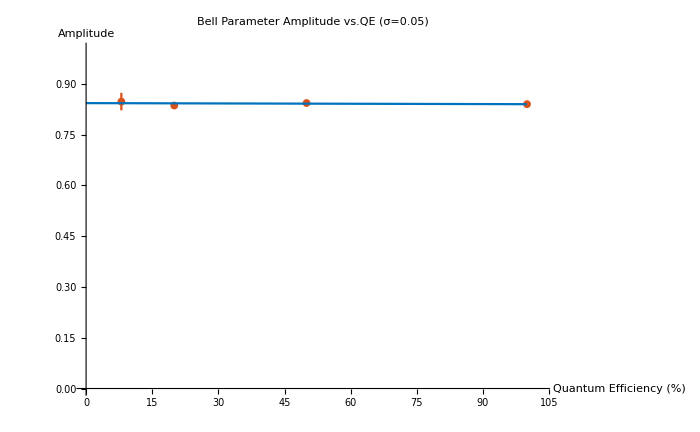

```mathematica
AmpR100 = nlmR100["ParameterTable"][[1,1,3,2]]; AmpR50 = nlmR50["ParameterTable"][[1,1,3,2]];AmpR20 = nlmR20["ParameterTable"][[1,1,3,2]]; AmpR8 = nlmR8["ParameterTable"][[1,1,3,2]];
AmpR100Err = nlmR100["ParameterTable"][[1,1,3,3]]; AmpR50Err = nlmR50["ParameterTable"][[1,1,3,3]];AmpR20Err = nlmR20["ParameterTable"][[1,1,3,3]]; AmpR8Err = nlmR8["ParameterTable"][[1,1,3,3]];
Amps = {{{100,AmpR100},ErrorBar[AmpR100Err]},{{50,AmpR50},ErrorBar[AmpR50Err]},{{20,AmpR20},ErrorBar[AmpR20Err]},{{8,AmpR8},ErrorBar[AmpR8Err]}};
FittedLine = LinearModelFit[Amps[[All,1]],QE,QE];
Show[ErrorListPlot[Amps,PlotRange->{{0,103},{0,1}},AxesStyle->Black,PlotStyle->Directive[RGBColor[0.85,0.325,0.098],PointSize[0.008]],AxesLabel->{HoldForm[Quantum Efficiency "(%)"],HoldForm[Amplitude]},PlotLabel->HoldForm[Bell Parameter Amplitude vs.QE (σ=0.05)],LabelStyle->{GrayLevel[0]},ImageSize->700],Plot[Normal[FittedLine],{QE,0,100},PlotStyle->
RGBColor[0,.447,.741],PlotLegends->Placed["A = "Normal[FittedLine],Below]]]
```

#### Change Dark Counts?:

```mathematica
D1E6 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B005_C2e+05_L01.txt","Data"][[2;;]];
D1E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-03_B005_C2e+05_L01.txt","Data"][[2;;]];
D2E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D2e-03_B005_C2e+05_L01.txt","Data"][[2;;]];
D5E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D5e-03_B005_C2e+05_L01.txt","Data"][[2;;]];
D1E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-02_B005_C2e+05_L01.txt","Data"][[2;;]];
D2E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D2e-02_B005_C2e+05_L01.txt","Data"][[2;;]];
D3E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D3e-02_B005_C1e+05_L01.txt","Data"][[2;;]];
```

```mathematica
nlmD1E6=NonlinearModelFit[D1E6,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD1E3=NonlinearModelFit[D1E3,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD2E3=NonlinearModelFit[D2E3,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD5E3=NonlinearModelFit[D5E3,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD1E2=NonlinearModelFit[D1E2,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD2E2=NonlinearModelFit[D2E2,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmD3E2=NonlinearModelFit[D3E2,(*Centre*)-Amplitude Cos[(*Frequency*) ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
```

D = 10^-6 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 7.36896×10^-18 | 0. | 1.
Amplitude | 0.830202 | 0.0178276 | 46.5684 | 2.96516×10^-101
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.00389201 | 0.0215927 | 0.180246 | 0.857165

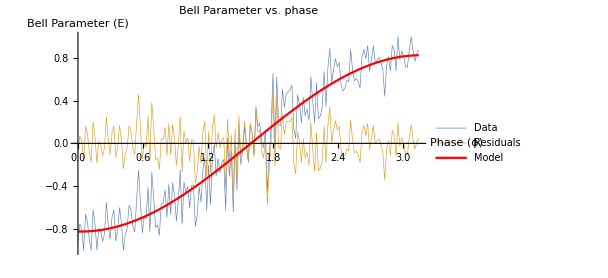
D = 10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 7.72924×10^-18 | 0. | 1.
Amplitude | 0.826117 | 0.0185823 | 44.4572 | 5.74325×10^-98
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0237675 | 0.022618 | -1.05082 | 0.294773

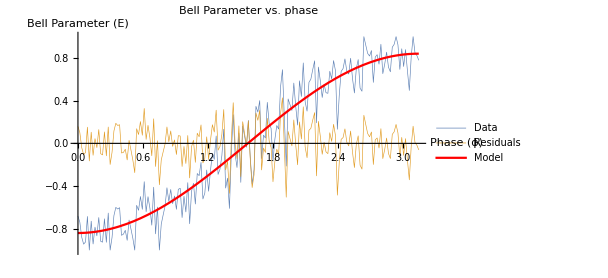
D = 2×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 4.16799×10^-18 | 0. | 1.
Amplitude | 0.839989 | 0.0182197 | 46.1032 | 1.53227×10^-100
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.0050424 | 0.0218106 | 0.231191 | 0.817434

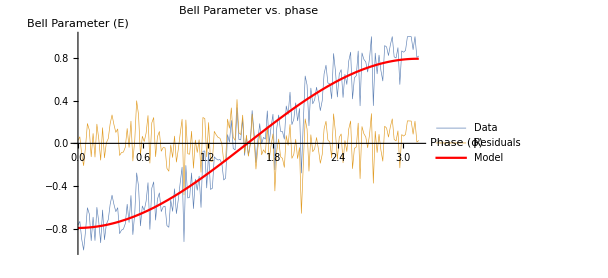
D = 5×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 4.96443×10^-18 | 0. | 1.
Amplitude | 0.792612 | 0.0176411 | 44.9298 | 1.02809×10^-98
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.00823279 | 0.0223802 | 0.36786 | 0.713417

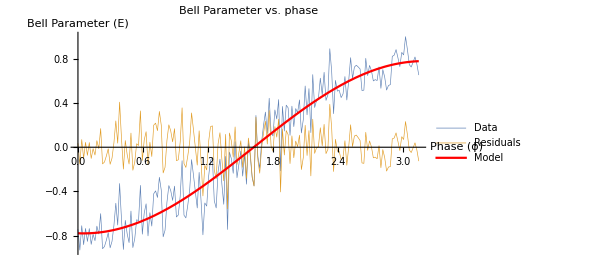
D = 10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 6.41921×10^-18 | 0. | 1.
Amplitude | 0.778886 | 0.017062 | 45.6505 | 7.68202×10^-100
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0495548 | 0.0220263 | -2.2498 | 0.0256934

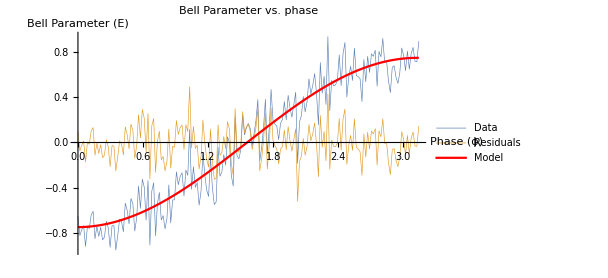
D = 2×10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 4.48664×10^-18 | 0. | 1.
Amplitude | 0.744616 | 0.0165822 | 44.9047 | 1.12621×10^-98
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.0119965 | 0.0223927 | 0.535731 | 0.592817

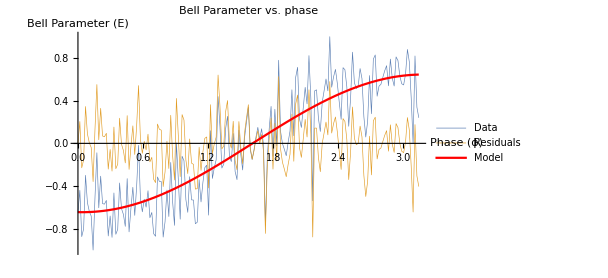
D = 3×10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 5.48173×10^-18 | 0. | 1.
Amplitude | 0.644766 | 0.026072 | 24.7302 | 2.5492×10^-59
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0390135 | 0.0406596 | -0.959516 | 0.338608

```mathematica
"D = 10^-6" nlmD1E6["ParameterTable"]Show[ListLinePlot[{D1E6,nlmD1E6["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD1E6],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"D = 10^-3" nlmD1E3["ParameterTable"]Show[ListLinePlot[{D1E3,nlmD1E3["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD1E3],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"D = 2×10^-3" nlmD2E3["ParameterTable"]Show[ListLinePlot[{D2E3,nlmD2E3["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD2E3],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"D = 5×10^-3" nlmD5E3["ParameterTable"]Show[ListLinePlot[{D5E3,nlmD5E3["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD5E3],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"D = 10^-2" nlmD1E2["ParameterTable"]Show[ListLinePlot[{D1E2,nlmD1E2["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD1E2],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"D = 2×10^-2" nlmD2E2["ParameterTable"]Show[ListLinePlot[{D2E2,nlmD2E2["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD2E2],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"D = 3×10^-2" nlmD3E2["ParameterTable"]Show[ListLinePlot[{D3E2,nlmD3E2["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmD3E2],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
```

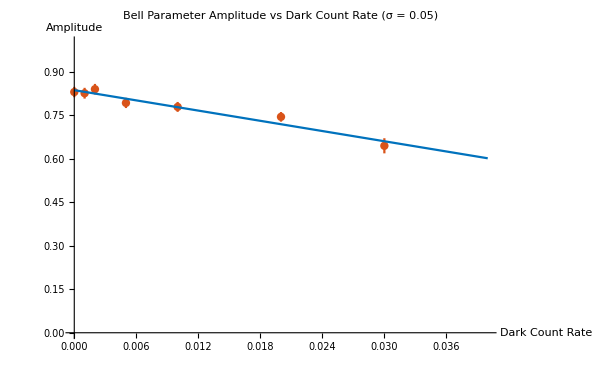

```mathematica
AmpD1E6 = nlmD1E6[[1,2,2,2]]; AmpD1E3 = nlmD1E3[[1,2,2,2]]; AmpD2E3 = nlmD2E3[[1,2,2,2]];  AmpD5E3 = nlmD5E3[[1,2,2,2]]; AmpD1E2 = nlmD1E2[[1,2,2,2]]; AmpD2E2 = nlmD2E2[[1,2,2,2]];  AmpD3E2 = nlmD3E2[[1,2,2,2]];
AmpD1E6Err = nlmD1E6["ParameterTable"][[1,1,3,3]]; AmpD1E3Err = nlmD1E3["ParameterTable"][[1,1,3,3]]; AmpD2E3Err = nlmD2E3["ParameterTable"][[1,1,3,3]]; AmpD5E3Err = nlmD5E3["ParameterTable"][[1,1,3,3]]; AmpD1E2Err = nlmD1E2["ParameterTable"][[1,1,3,3]]; AmpD2E2Err = nlmD2E2["ParameterTable"][[1,1,3,3]]; AmpD3E2Err = nlmD3E2["ParameterTable"][[1,1,3,3]];
Amps = {{{10^-6,AmpD1E6},ErrorBar[AmpD1E6Err]},{{10^-3,AmpD1E3},ErrorBar[AmpD1E3Err]},{{2 10^-3,AmpD2E3},ErrorBar[AmpD2E3Err]},{{5 10^-3,AmpD5E3},ErrorBar[AmpD5E3Err]},{{10^-2,AmpD1E2},ErrorBar[AmpD1E2Err]},{{2 10^-2,AmpD2E2},ErrorBar[AmpD2E2Err]},{{3 10^-2,AmpD3E2},ErrorBar[AmpD3E2Err]}};
FittedLine = NonlinearModelFit[Amps[[All,1]],a+b D,{a,b,c,d,e},D];
Show[ErrorListPlot[Amps,PlotRange->{{0,4 10^-2},{0,1}},PlotStyle->Directive[RGBColor[.85,.325,.098],PointSize[0.01]],AxesLabel->{"Dark Count Rate","Amplitude"},PlotLabel->"Bell Parameter Amplitude vs Dark Count Rate (σ = 0.05)",LabelStyle->{GrayLevel[0]},ImageSize->600],Plot[Normal[FittedLine],{D,0,0.04},PlotStyle->RGBColor[0,.447,.741],PlotLegends->Placed["A = "Normal[FittedLine],Bottom]]]
```

#### Change Blur:

```mathematica
B00 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B0_C2e+05_L01.txt","Data"][[2;;]];
B05 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B005_C2e+05_L01.txt","Data"][[2;;]];
B10 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B01_C2e+05_L01.txt","Data"][[2;;]];
B15 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B015_C2e+05_L01.txt","Data"][[2;;]];
B20 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B02_C2e+05_L01.txt","Data"][[2;;]];
B25 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B025_C2e+05_L01.txt","Data"][[2;;]];
B30 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Corrected Data\\R8_D1e-06_B03_C2e+05_L01.txt","Data"][[2;;]];
```

```mathematica
nlmB00 = NonlinearModelFit[B00,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmB05 = NonlinearModelFit[B05,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmB10 = NonlinearModelFit[B10,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmB15 = NonlinearModelFit[B15,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmB20 = NonlinearModelFit[B20,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmB25 = NonlinearModelFit[B25,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
nlmB30 = NonlinearModelFit[B30,(*Centre*)-Amplitude Cos[(*Frequency*)ϕ + Phase],{{Centre,0},Amplitude,Frequency,Phase},ϕ];
```

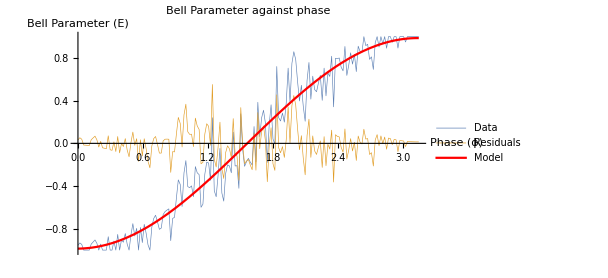
σ = 0.00 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 2.19657×10^-18 | 0. | 1.
Amplitude | 0.986185 | 0.0157199 | 62.735 | 7.62733×10^-123
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.0102381 | 0.0160283 | 0.638752 | 0.52381

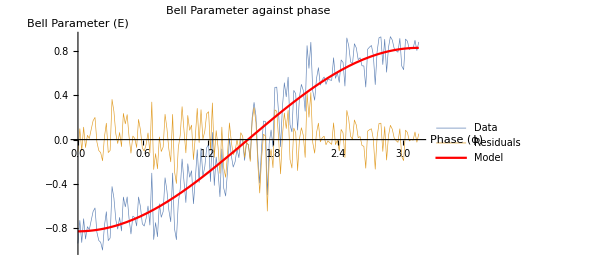
σ = 0.05 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 7.36896×10^-18 | 0. | 1.
Amplitude | 0.830202 | 0.0178276 | 46.5684 | 2.96516×10^-101
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.00389201 | 0.0215927 | 0.180246 | 0.857165

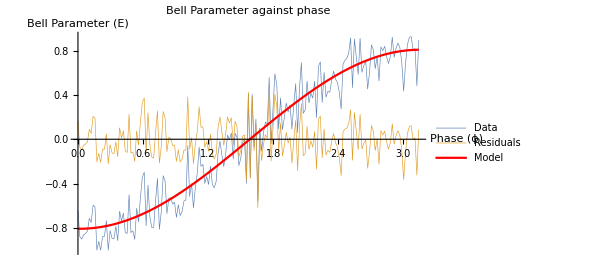
σ = 0.10 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.16701×10^-17 | 0. | 1.
Amplitude | 0.807411 | 0.0177109 | 45.5884 | 9.59089×10^-100
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0140434 | 0.0220568 | -0.636689 | 0.52515

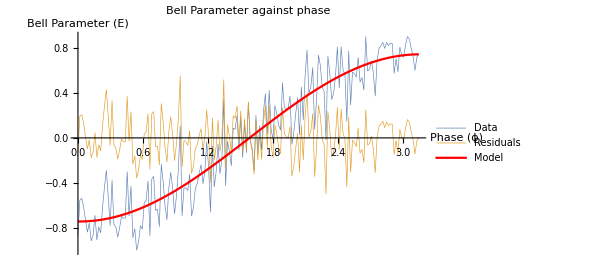
σ = 0.15 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.843×10^-18 | 0. | 1.
Amplitude | 0.745006 | 0.0196787 | 37.8585 | 8.65876×10^-87
Frequency | 1. | 0. | ∞ | 0.
Phase | -0.0106314 | 0.0265604 | -0.400274 | 0.689438

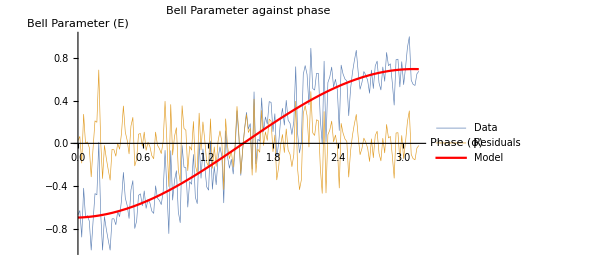
σ = 0.20 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 7.5667×10^-18 | 0. | 1.
Amplitude | 0.696026 | 0.0211426 | 32.9206 | 2.23477×10^-77
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.0463347 | 0.0305436 | 1.517 | 0.13105

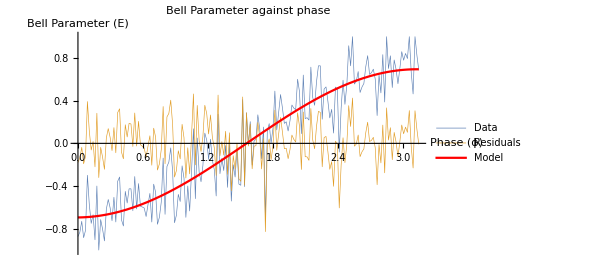
σ = 0.25 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.34451×10^-17 | 0. | 1.
Amplitude | 0.69415 | 0.0222225 | 31.2364 | 6.2567×10^-74
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.016253 | 0.0321911 | 0.50489 | 0.614264

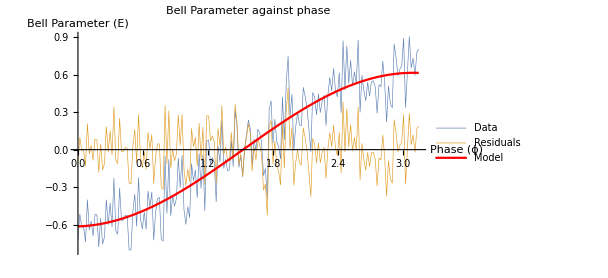
σ = 0.30 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0. | 1.35403×10^-17 | 0. | 1.
Amplitude | 0.615384 | 0.0187538 | 32.8138 | 3.66554×10^-77
Frequency | 1. | 0. | ∞ | 0.
Phase | 0.048502 | 0.030643 | 1.58281 | 0.11525

```mathematica
"σ = 0.00" nlmB00["ParameterTable"]Show[ListLinePlot[{B00,nlmB00["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB00],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"σ = 0.05" nlmB05["ParameterTable"]Show[ListLinePlot[{B05,nlmB05["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB05],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"σ = 0.10" nlmB10["ParameterTable"]Show[ListLinePlot[{B10,nlmB10["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB10],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"σ = 0.15" nlmB15["ParameterTable"]Show[ListLinePlot[{B15,nlmB15["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB15],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"σ = 0.20" nlmB20["ParameterTable"]Show[ListLinePlot[{B20,nlmB20["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB20],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"σ = 0.25" nlmB25["ParameterTable"]Show[ListLinePlot[{B25,nlmB25["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB25],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
"σ = 0.30" nlmB30["ParameterTable"]Show[ListLinePlot[{B30,nlmB30["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmB30],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{"Phase (ϕ)","Bell Parameter (E)"},PlotLabel->"Bell Parameter vs. phase"]
```

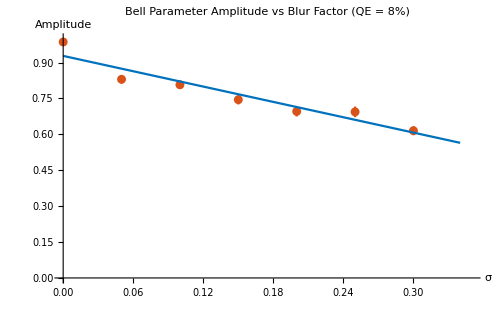

```mathematica
AmpB00 = nlmB00[[1,2,2,2]]; AmpB00Err =nlmB00["ParameterErrors"][[2]]; AmpB05 = nlmB05[[1,2,2,2]]; AmpB05Err =nlmB05["ParameterErrors"][[2]]; AmpB10 = nlmB10[[1,2,2,2]]; AmpB10Err =nlmB10["ParameterErrors"][[2]]; AmpB15 = nlmB15[[1,2,2,2]];  AmpB15Err =nlmB15["ParameterErrors"][[2]]; AmpB20 = nlmB20[[1,2,2,2]]; AmpB20Err =nlmB20["ParameterErrors"][[2]];  AmpB25 = nlmB25[[1,2,2,2]]; AmpB25Err =nlmB25["ParameterErrors"][[2]];  AmpB30 = nlmB30[[1,2,2,2]]; AmpB30Err =nlmB30["ParameterErrors"][[2]];
Amps = {{{0,AmpB00},ErrorBar[AmpB00Err]},{{0.05,AmpB05},ErrorBar[AmpB05Err]},{{0.10,AmpB10},ErrorBar[AmpB10Err]},{{0.15,AmpB15},ErrorBar[AmpB15Err]},{{0.20,AmpB20},ErrorBar[AmpB20Err]},{{0.25,AmpB25},ErrorBar[AmpB25Err]},{{0.3,AmpB30},ErrorBar[AmpB30Err]}};
FittedLine = NonlinearModelFit[Amps[[All,1]],a+b σ ,{a,b},σ];
Show[ErrorListPlot[Amps,PlotRange->{{0,0.35},{0,1}},AxesStyle->Black,PlotStyle->RGBColor[.85,.325,.098],AxesLabel->{"σ","Amplitude"},PlotLabel->"Bell Parameter Amplitude vs Blur Factor (QE = 8%)",LabelStyle->{GrayLevel[0]},ImageSize->500],Plot[Normal[FittedLine],{σ,0,0.34},PlotStyle->RGBColor[0,.447,.741],PlotLegends->Placed["A = "Normal[FittedLine],Below]]]
```

## New Functions

```mathematica
sample = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8_D1e-06_B001_C1e+06_L01.txt","Data"][[2;;]];
nlmsample = NonlinearModelFit[sample,Subscript[μ, Ε]-Subscript[Ε, ο] Cos[k ϕ + θ],{Subscript[Ε, ο],{Subscript[μ, Ε],0},k,θ},ϕ];
```

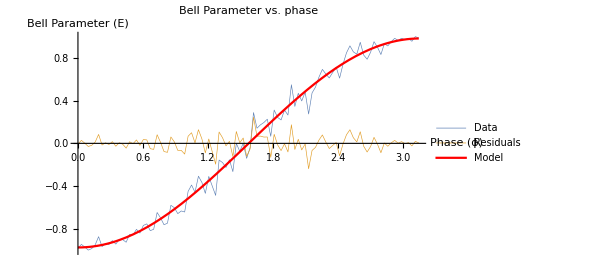
QE = 8% (2) -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Ε_ο | 0.97888 | 0.0211826 | 46.2114 | 2.16499×10^-67
μ_Ε | 0.00374622 | 0.0165122 | 0.226876 | 0.821002
k | 0.996714 | 0.0382352 | 26.0679 | 2.43125×10^-45
θ | -0.00159361 | 0.0643764 | -0.0247546 | 0.980302

```mathematica
"QE = 8% (2)" nlmsample["ParameterTable"]Show[ListLinePlot[{sample,nlmsample["FitResiduals"]},PlotLegends->{"Data","Residuals"},DataRange->{0,π},PlotStyle->Directive[Thickness[.001]],ImageSize->450],Plot[Normal[nlmsample],{ϕ,0,π},PlotStyle->Red,PlotLegends->{"Model"}],AxesLabel->{Style["Phase (ϕ)",Black,15],Style["Bell Parameter (E)",Black,15]},PlotLabel->Style["Bell Parameter vs. phase",Black,20]]
```